Coded by Manish J. Thapa for Advanced Kinteics class at ETH Zurich

## Def.

```mathematica
Clear[ψ]
```

```mathematica
Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

```mathematica
ψ[x_]:=(2π a^2)^(-1/4) Exp[-x^2/(4a^2)];
```

```mathematica
A=InverseFourierTransform[ψ[x],x,k]//FullSimplify
```

√(1/a^2) (a^2)^(3/4) ⅇ^(-a^2 k^2) (2/π)^(1/4)

```mathematica
param={a->1,ω->(ℏ k^2)/(2m),m->1,ℏ ->1};(*for simplicity and fast numerical convergence, evrything is in atomic units*)
```

## 2.2

```mathematica
Subscript[ψ, ∞]=Assuming[Im[t]<2,Integrate[A Exp[I k x]Exp[-I t ω]//.param,{k,-Infinity,Infinity}]]
```

(2^(3/4) ⅇ^((ⅈ x^2)/(2 (-2 ⅈ+t))) π^(1/4))/(√(2+ⅈ t))

```mathematica
Subscript[ψ, k]=Integrate[A Exp[I k x]Exp[-I t ω]//.param,{k,-1/(4),1/(4)}]
```

-((-1)^(3/4) ⅇ^((ⅈ x^2)/(2 (-2 ⅈ+t))) (π/2)^(1/4) (Erf[((1/8+ⅈ/8) (-2 ⅈ+t-4 x))/(√(-2 ⅈ+t))]+Erf[((1/8+ⅈ/8) (-2 ⅈ+t+4 x))/(√(-2 ⅈ+t))]))/(√(-2 ⅈ+t))

```mathematica
Subscript[Norm, 1]=Integrate[Abs[Subscript[ψ, ∞]//.{t->0}]^2,{x,-Infinity,Infinity}] (*Test for Normalization*)
```

2 π

```mathematica
Subscript[Norm, 2]=NIntegrate[Abs[Subscript[ψ, k]//.{t->0}]^2,{x,-Infinity,Infinity},Method->"MonteCarlo"](*Test for Normalization, Numerical integration*)
```

```mathematica
Subscript[ψ, k]=Integrate[A Exp[I k x]Exp[-I t ω]//.param,{k,-1/(4),1/(4)}]
```

-((-1)^(3/4) ⅇ^((ⅈ x^2)/(2 (-2 ⅈ+t))) (π/2)^(1/4) (Erf[((1/8+ⅈ/8) (-2 ⅈ+t-4 x))/(√(-2 ⅈ+t))]+Erf[((1/8+ⅈ/8) (-2 ⅈ+t+4 x))/(√(-2 ⅈ+t))]))/(√(-2 ⅈ+t))

2.39747

```mathematica
Plot1=Plot[(1/Subscript[Norm, 1])Abs[Subscript[ψ, ∞]//.{t->0}]^2,{x,-50,50},PlotRange->All,PlotStyle->Blue];
```

```mathematica
Plot2=Plot[(1/Subscript[Norm, 2])Abs[Subscript[ψ, k]//.{t->0}]^2,{x,-50,50},PlotRange->All,PlotStyle->Green];
```

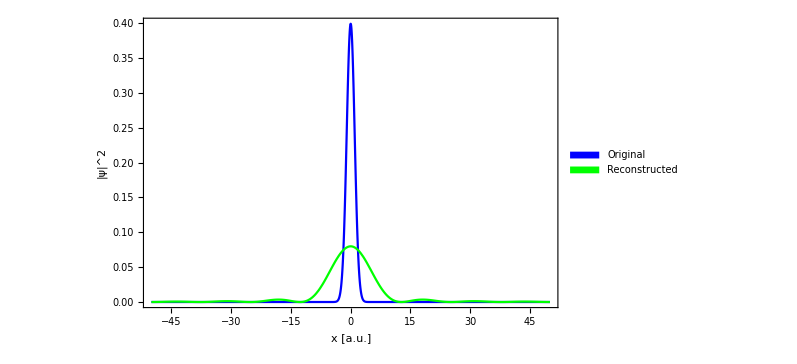

```mathematica
Legended[Show[Plot1,Plot2,AxesStyle->Black,FrameLabel->{"x [a.u.]","|ψ|^2"},Frame->True,FrameTicks->All,ImageSize->590,PlotRange->All,BaseStyle->{12,FontFamily->"Helvetica"}],Placed[SwatchLegend[{Blue,Green},{Style["Original",12],Style["Reconstructed",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.7,0.1},{0,0}}]]
```

## 2.3

```mathematica
data1=Table[(1/Subscript[Norm, 2])Abs[Subscript[ψ, k]]^2,{x,-90,90,1},{t,0,500,10}];
```

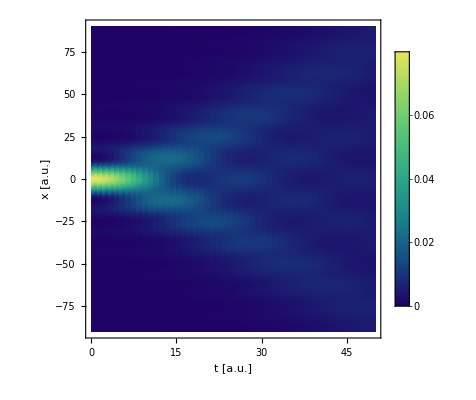

```mathematica
p1=ListDensityPlot[data1,ColorFunction->"BlueGreenYellow", FrameLabel->{"t [a.u.]","x [a.u.]"},PlotLegends->Automatic,PlotRange->All,DataRange->{{0,50},{-90,90}}]
```

```mathematica
(*this wave packet as zero group velocity, as in the k-sapce , it is centered at 0, and hence average momentum is 0*)
```

```mathematica
Export["exportP1.png",p1]
```

exportP1.png

```mathematica
Clear[Subscript[ψ, shift]];
```

## 2.4

```mathematica
Subscript[ψ, shift][x_]:=(2π (a^2))^(-1/4) Exp[-(x^2)/(2a^2)]Exp[I 2 a x];(*can also try with Subscript[k, 0]=1/10, the shift is almost negligible though, the point is to see wavepacket traveling in time towards x at velocity given by group velocity*)
```

```mathematica
B=InverseFourierTransform[Subscript[ψ, shift][x],x,k]//FullSimplify
```

((a^2)^(1/4) ⅇ^(-1/2 a^2 (-2 a+k)^2))/(2 π)^(1/4)

```mathematica
Subscript[ψ, shift]=Integrate[B Exp[I k x]Exp[-I t ω]//.param,{k,-1/4,1/4}]//FullSimplify
```

-((-1)^(3/4) ⅇ^((-4 t+(4+ⅈ x) x)/(2 (-ⅈ+t))) π^(1/4) (Erf[((1/8+ⅈ/8) (7 ⅈ+t-4 x))/(√(-ⅈ+t))]+Erf[((1/8+ⅈ/8) (-9 ⅈ+t+4 x))/(√(-ⅈ+t))]))/(2^(3/4) √(-ⅈ+t))

```mathematica
Subscript[Norm, 3]=NIntegrate[Abs[Subscript[ψ, shift]//.{t->0}]^2,{x,-Infinity,Infinity},Method->"MonteCarlo"](*Test for Normalization, Numerical integration*)
```

0.0260385

```mathematica
Plot3=Plot[(1/Subscript[Norm, 2]) Abs[Subscript[ψ, k]//.{t->40}]^2,{x,-15,15},PlotRange->All,PlotStyle->Blue];
```

```mathematica
Plot4=Plot[(1/Subscript[Norm, 3])Abs[Subscript[ψ, shift]//.{t->40}]^2,{x,-15,15},PlotRange->All,PlotStyle->Green];
```

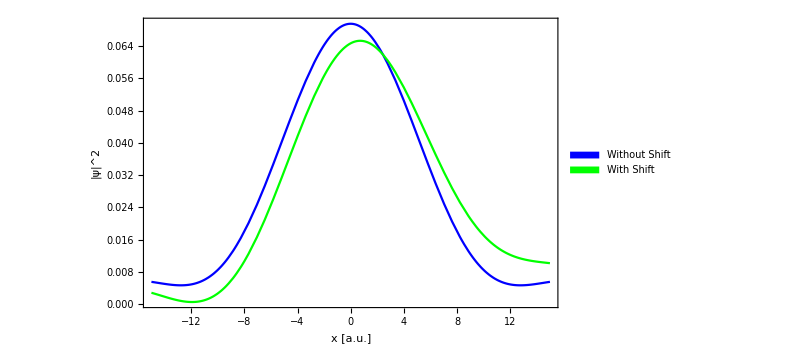

```mathematica
Legended[Show[Plot3,Plot4,AxesStyle->Black,FrameLabel->{"x [a.u.]","|ψ|^2"},Frame->True,FrameTicks->All,ImageSize->590,PlotRange->All,BaseStyle->{12,FontFamily->"Helvetica"}],Placed[SwatchLegend[{Blue,Green},{Style["Without Shift",12],Style["With Shift",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.7,0.1},{0,0}}]]
```

```mathematica
(*as you can see the wave packet moves towards the positive x-direction in each time step, this is because the gaussian wavepacket is no longer centered at k=0, plot your wavepacket amplitudes in k-space*)
```

```mathematica
data2=Table[(1/Subscript[Norm, 3])Abs[Subscript[ψ, shift]]^2,{x,-90,90,1},{t,0,500,10}];
```

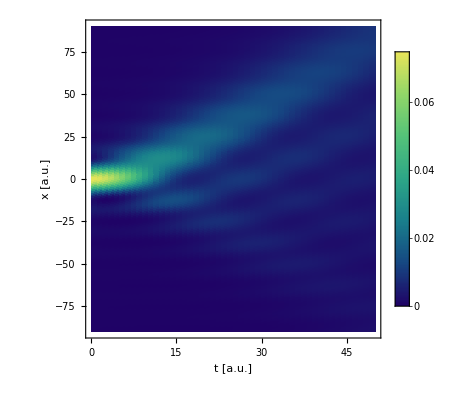

```mathematica
p2=ListDensityPlot[data2,ColorFunction->"BlueGreenYellow", FrameLabel->{"t [a.u.]","x [a.u.]"},PlotLegends->Automatic,PlotRange->All,DataRange->{{0,50},{-90,90}}]
```

```mathematica
(*taking the expectation value of x in each time step, you will see that all these expectation values lie in the greener region. the gradient of the line formed by joining those points will give you group velocity*)
```

```mathematica
Export["exportP2.png",p2]
```

exportP2.png